# MUSIC RNN

## Importing Data

```mathematica
midi=Import["C:\\Users\\Likith Palabindela\\Downloads\\song1.mid","SoundNotes"]
```

{{},7,{SoundNote[BassDrum2,{0.,0.0714275},SoundVolume→0.941176],SoundNote[BassDrum2,{0.85713,0.928557},SoundVolume→0.941176],1360,SoundNote[HiHatClosed,{264.567,264.639},SoundVolume→0.0784314],SoundNote[HiHatClosed,{264.853,264.925},SoundVolume→0.054902]}}
 |  |  |  |

```mathematica
Length@midi
```

9

```mathematica
midi=Delete[midi,1]
```

{{SoundNote[C5,{0.,0.142855},Harpsichord,SoundVolume→0.996078],SoundNote[D#5,{0.28571,0.428565},Harpsichord,SoundVolume→0.996078],750,SoundNote[F#4,{264.567,264.71},Harpsichord,SoundVolume→0.0392157],SoundNote[G4,{264.853,264.996},Harpsichord,SoundVolume→0.00784314]},{1},4,{1},{1}}
 |  |  |  |

```mathematica
Length@midi
```

8

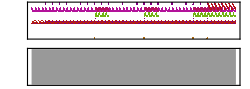

```mathematica
Sound@Flatten@midi
```

## Formatting Data

```mathematica
harpischord=midi[[1]];
```

```mathematica
notes=Table[harpischord[[x]][[1]],{x,1,Length[harpischord]}]
```

{C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4}

```mathematica
notelist=Flatten@Characters@notes;
```

## Building the Network

```mathematica
enc=NetEncoder[{"Characters",Union@Characters@notelist}]
```

NetEncoder[<>]

```mathematica
Union@Characters@ToString@notelist
```

{#,{,},,, ,4,5,C,D,F,G}

```mathematica
"#"
```

#

```mathematica
Union@Flatten@Union@Characters@notes
```

{#,4,5,C,D,F,G}

```mathematica
net=NetChain[{
UnitVectorLayer[],
GatedRecurrentLayer[128],
GatedRecurrentLayer[128],
SequenceLastLayer[],
LinearLayer[11],
SoftmaxLayer[]},
"Input"->enc]
```

NetChain[<>]

```mathematica
threadnotes=Table[Thread[{notelist[[;;n]]}->notelist[[n+1]]],{n, 47,Length@notes-1}]
```

{{{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4}→G},705,{{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,697,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4}→G}}
 |  |  |  |

```mathematica
threadnotes=Flatten[threadnotes,1]
```

{1}
 |  |  |  |

```mathematica
trainednet=NetTrain[net,threadnotes,BatchSize->64,MaxTrainingRounds->20,TargetDevice->{"GPU",1}]
```

NetTrain::encgenfail1: Could not encode input number 1 for port "Input": input was not a string. Please check the example.

$Failed

```mathematica
threadnotes[[1;;5]]
```

{{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4}→G,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G}→4,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4}→G,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G}→#,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#}→4}

```mathematica
{"C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#","4","G","4","G","#","4","G","4","F","#","4","G","4","C","5","D","#","5","G","4","G","#","4","C","5","G","#","4"}
```

```mathematica
ToString[threadnotes[[1]][[1]]]->threadnotes[[1]][[2]]
```

{C, 5, D, #, 5, G, 4, G, #, 4, C, 5, G, #, 4, G, 4, G, #, 4, G, 4, G, #, 4, G, 4, F, #, 4, G, 4, C, 5, D, #, 5, G, 4, G, #, 4, C, 5, G, #, 4}→G

```mathematica
threadnotes[[All,2]]
```

{G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4,C5,D#5,G4,G#4,C5,G#4,G4,G#4,G4,G#4,G4,F#4,G4}

```mathematica
threadnotes[[1;;5]]
```

```mathematica
{{"C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#","4","G","4","G","#","4","G","4","F","#","4","G","4","C","5","D","#","5","G","4","G","#","4","C","5","G","#","4"}->"G",{"C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#","4","G","4","G","#","4","G","4","F","#","4","G","4","C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G"}->"4",{"C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#","4","G","4","G","#","4","G","4","F","#","4","G","4","C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4"}->"G",{"C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#","4","G","4","G","#","4","G","4","F","#","4","G","4","C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G"}->"#",{"C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#","4","G","4","G","#","4","G","4","F","#","4","G","4","C","5","D","#","5","G","4","G","#","4","C","5","G","#","4","G","4","G","#"}->"4"}
```

{{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4}→G,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G}→4,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4}→G,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G}→#,{C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#,4,G,4,G,#,4,G,4,F,#,4,G,4,C,5,D,#,5,G,4,G,#,4,C,5,G,#,4,G,4,G,#}→4}

```mathematica
Import["D:\\downloads\\fashion_captions.wdx"]
```